```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["naloga01/praznenjeKondenzatorja.txt","Table"];
```

```mathematica
data2=data*1.1;
data3=Transpose[{Transpose[data][[1]],Transpose[data][[1]]*1000}];
```

```mathematica
(*
Kako naredimo graf s skupnimi osmi (subplot)?
    - vsi grafi morajo meti enako veliko obrobo - ImagePadding
      - odstranimo tekst za tiste osi, kjer ga ne potrebujemo - npr. FrameTicksStyle->{Automatic,Directive[FontOpacity->0,FontSize->0]
*)
```

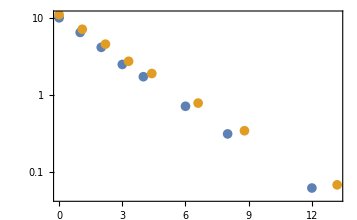

```mathematica
(* Zgornja grafa - nocemo teksta spodaj (a padding rabimo isti kot spodaj!) *)
p1=p2=ListLogPlot[{data,data2},Frame->True,FrameTicksStyle->{Automatic,Directive[FontOpacity->0,FontSize->0]},ImagePadding->{{30,1},{30,1}}]
```

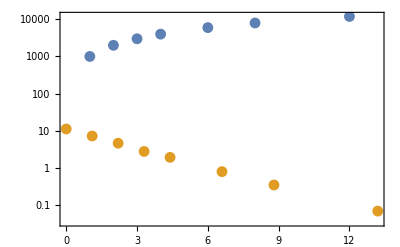

```mathematica
(* Spodnji graf - pove nam potreben ImagePadding, da vse se pride na sliko, po potrebi gledamo se zgornje grafe - vsi morajo imeti enako! *)
p3=ListLogPlot[{data3,data2},Frame->True,ImagePadding->{{30,1},{30,1}}]
```

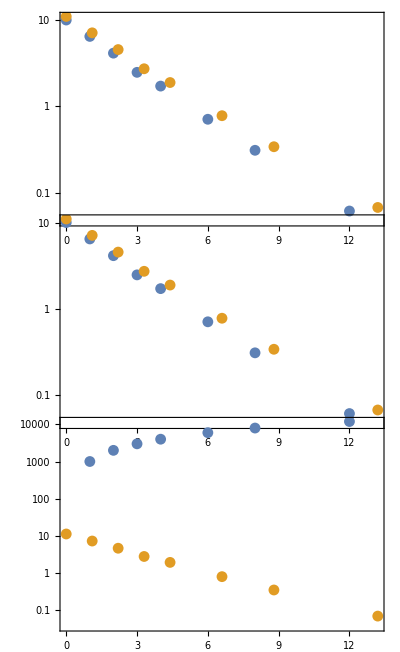

```mathematica
(* Uporabimo GraphicsGrid in jih zdruzimo. Z negativnim Spacings jih "potlacimo" skupaj po potrebi (priblizno kot smo nastavili padding) *)
GraphicsGrid[{{p1},{p2},{p3}},Spacings->-40]
```